```mathematica
Integrate[(1+p)^(-1/2),p]
```

2 √(1+p)

```mathematica
Integrate[2/(Sqrt[1+x^2]) ,x]
```

2 ArcSinh[x]

```mathematica
Integrate[-N * (1/(x-1)),x]
```

-N Log[-1+x]

```mathematica
Simplify[p+Sqrt[1+p^2]]
```

p+√(1+p^2)

```mathematica
Integrate[y, x]
```

x y

```mathematica
Simplify[(1/2)(((
(1-x)^(1-n))/1-n) - (((1-x)^(n+1))/n+1))]
```

1/2 (-1-n+(1-x)^(1-n)-(1-x)^(1+n)/n)

```mathematica
(1/2)(((1-x)^(1-n)/(1-n)) - ((1-x)^(n+1)/(1+n)))
```

1/2 ((1-x)^(1-n)/(1-n)-(1-x)^(1+n)/(1+n))

```mathematica
Simplify[(1/2)(((1-x)^(1-n)/(1-n)) - ((1-x)^(n+1)/(1+n)))]
```

1/2 ((1-x)^(1-n)/(1-n)-(1-x)^(1+n)/(1+n))

```mathematica
Integrate[(1/2)((1-x)^(-n) - (1-x)^n),x]
```

1/2 ((1-x)^-n (1/(-1+n)+x/(1-n))-(1-x)^n (-1/(1+n)+x/(1+n)))

```mathematica
(1/2)((1-x)^(-n) - (1-x)^n)
```

1/2 ((1-x)^-n-(1-x)^n)

```mathematica
Simplify[1/2 ((1-x)^-n (1/(-1+n)+x/(1-n))-(1-x)^n (-1/(1+n)+x/(1+n)))]
```

((1+n-(1-x)^(2 n)+n (1-x)^(2 n)) (1-x)^(1-n))/(2 (-1+n^2))

```mathematica
Pursuit[x_, n_] := 1/2(1-x)((1-x)^n/(1+n)- (1-x)^-n/(1-n))+n/(1-n^2)
```

```mathematica
Pursuit[23]
```

112.874-8.8842 ⅈ

```mathematica
n = 0.98
```

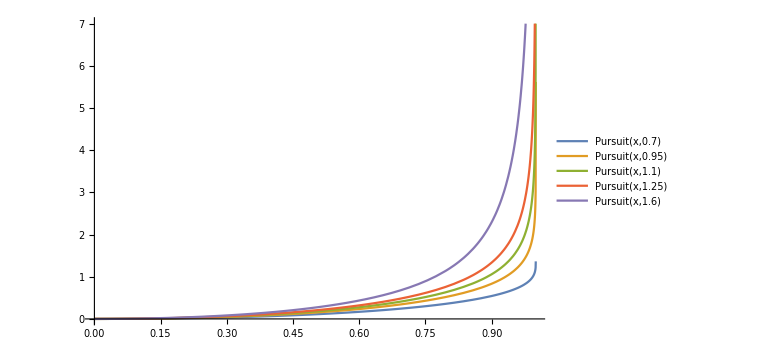

```mathematica
Plot[{Pursuit[x, .70],Pursuit[x, .95],Pursuit[x, 1.1],Pursuit[x, 1.25],Pursuit[x, 1.6] }, {x,0,1}, ImageSize->Large, PlotRange->{0,7}, PlotLegends->"Expressions" ]
```

```mathematica
n = 0.99
```

0.99